# DATA TRANSFORMATION

## Table of content

Click on the links below to go to the relevant sections.

Introduction

Generating data

Descriptive statistics

Data visualization

Testing assumptions for the use of parametric tests

Nonlinear transformations

Log transform

Square root transform

Comparing means

## Introduction

In this notebook, we explore data transformation.  It is the process of using a mathematical function to change each value in a set of values.

Data transformation is used when the data fails to meet the assumption of normality for the use of parametric tests.   This assumption states that the data is taken from a population in which the values for the variable under consideration is normally distributed.

We start the notebook by generating data and then investigate it using summary statistics.

## Generating data

In the code cell below, we use the SeedRandom function to seed the pseudorandom number generator.  This ensures that the same random values are generated each time the cell is evaluated.  We set a sample size of 200 for each group and generate random values for a variable for each of two groups, named varGroupA and varGroupB.

For the variable in group A we take random values from a normal distribution with a mean, μ=10, and a standard deviation σ=1.  We add random noise to these values for group B.  The random noise is taken from a χ^2 distribution with ν=5 degrees of freedom.  We subtract 5 from each value to bring the average in both group to approximately the same value.

```mathematica
SeedRandom[17];
n=200;
varGroupA=RandomReal[NormalDistribution[10,1],n];
varGroupB=varGroupA+RandomReal[ChiSquareDistribution[5],n]-5;
```

## Descriptive statistics

Our first task in understanding the data involves summary statistics.  We create a utility function named describe, to calculate the mean, standard deviation, median, and interquartile range of a list passed to it as parameter.

```mathematica
describe[v_List]:={Mean[v],StandardDeviation[v],Median[v],InterquartileRange[v]}
```

We can express these summary statistics using the TableForm function with table headings.

```mathematica
TableForm[describe/@{varGroupA,varGroupB},TableHeadings->{None,{"Mean","Standard deviation","Median","Interquartile range"}}]
```

Mean | Standard deviation | Median | Interquartile range
9.94615 | 1.00576 | 9.88286 | 1.51017
10.2026 | 3.23585 | 9.61579 | 4.14699

## Data visualization

The next step in understanding the data is visualization.  A box-and-whisker plot gives us an understanding of the distribution of values for the variable in each group.  In FIGURE 1 we use the BoxWhiskerChart function to create the plot.

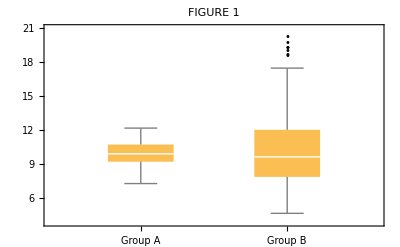

```mathematica
BoxWhiskerChart[{varGroupA,varGroupB},"Outliers",PlotLabel->"FIGURE 1",ChartLabels->{"Group A","Group B"}]
```

We can get further understanding of data through visualizing the frequency distribution.  We can create either histogram or a smooth histogram using the PairedHistogram and PairedSmoothHistogram functions.  The results are in Figure 2A and Figure 2B.

```mathematica
PairedHistogram[varGroupA,varGroupB,PlotLabel->"FIGURE 2A",ChartLabels->{"Group A","Group B"}]
```

-Graphics-

```mathematica
PairedSmoothHistogram[Tooltip[varGroupA,"Group A"],Tooltip[varGroupB,"Group B"],PlotLabel->"FIGURE 2B",Filling->Axis]
```

-Graphics-

We generated the data such that the values for our variable under consideration is not from a normal distribution.  We can see this in the data visualization above.  The Skewness function confirms the long right tail in group B (positive skewness).

```mathematica
Skewness/@{varGroupA,varGroupB}
```

{0.0307934,0.826874}

## Testing assumptions for the use of parametric tests

Our aim is to investigate the difference in the variable values between the trow groups.  One way to achieve this aim is to compare the means.  This is done using a t test.  A t test is a parametric test.  To use a parametric test requires the data to adhere to certain assumptions.  In this notebook we restrict ourselves to determining if the data values are from a population in which the variable is normally distributed.  We can investigate this using quantile plots and statistical tests such as the Shapiro-Wilk test.  Figure 3A shows a quantile plot for group A and Figure 3B shows the same plot for group B.  In the case of the latter, we see an obvious deviation.

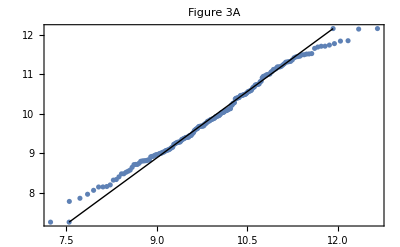

```mathematica
QuantilePlot[varGroupA,PlotLabel->"Figure 3A"]
```

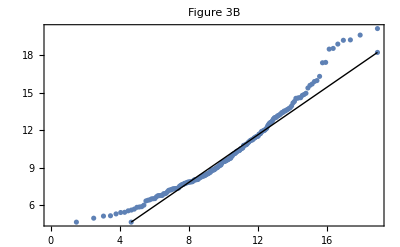

```mathematica
QuantilePlot[varGroupB,PlotLabel->"Figure 3B"]
```

In the two code cells below, we use the Shapiro-Wilk test for each of the groups.  The null hypothesis for this test states that the data is from a population in which the variable is normally distributed.

```mathematica
ShapiroWilkTest[varGroupA,"TestDataTable"]
```

| Statistic | P-Value
Shapiro-Wilk | 0.988444 | 0.10509

```mathematica
ShapiroWilkTest[varGroupB,"TestDataTable"]
```

| Statistic | P-Value
Shapiro-Wilk | 0.95033 | 2.03058×10^-6

We note rejection of the null hypothesis in the case of group B, as expected from the original generation of the data.  We conclude that the assumptions for the use of parametric tests are not met.

## Nonlinear transformations

While we advocate for the use of nonparametric tests such as the Mann-Whitney test in this case, it is also possible to perform non-linear transformations of the data.  These transformation alter the distribution of the data, with an aim that the transformed data adheres to the assumptions for the use of parametric tests.

Three examples of transformations are the log transform, the square root, and the inverse cosine function.  Figure 4 displays the log base 10 and the square root transformations for the data in group B.

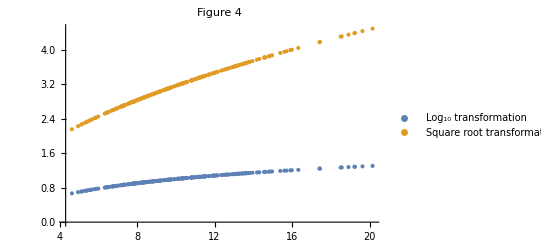

```mathematica
ListPlot[{Thread[{varGroupB,Log10[varGroupB]}],Thread[{varGroupB,Sqrt[varGroupB]}]},PlotLegends->{"Log_10 transformation","Square root transformation"},PlotLabel->"Figure 4"]
```

### Log transform

Log transformations are used for continuous numerical variables.  Logarithmic function are only defined for positive values.  If the data contains values of zero or less, a linear transformation will be required prior to the log transformation.

The logarithm function can have any base.  Base e logarithm (termed the natural logarithm, denoted by ln) and base 10 logarithm (denoted by log) differ by a constant as seen in the scatter plot in Figure 5 and both are in common use.  The Log10 function performs log base 10 transforms and the Log function performs the natural logarithm transform.

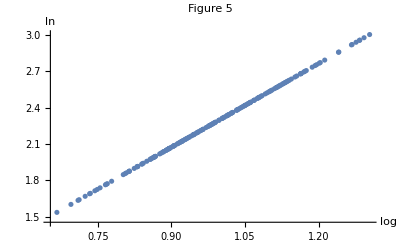

```mathematica
ListPlot[Thread[{Log10[varGroupB],Log[varGroupB]}],PlotLabel->"Figure 5",AxesLabel->{"log","ln"}]
```

Figure 6A and Figure 6B shows a histogram of the data for group B transformed using log base 10 and the natural logarithm respectively.

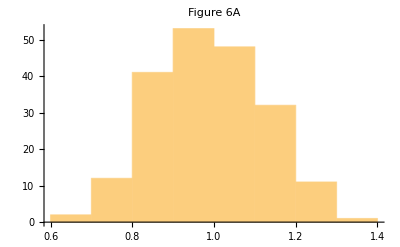

```mathematica
Histogram[Log10[varGroupB],PlotLabel->"Figure 6A",ChartLegends->"log transformation"]
```

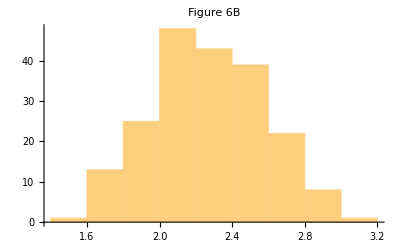

```mathematica
Histogram[Log[varGroupB],PlotLabel->"Figure 6B",ChartLegends->"ln transformation"]
```

In both cases, the frequency distribution appears more bell-shaped.  Figure 7A and Figure 7B shows the quantile plots of the transformed data.

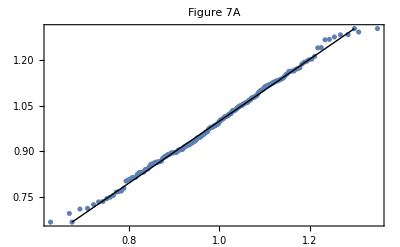

```mathematica
QuantilePlot[Log10@varGroupB,PlotLabel->"Figure 7A"]
```

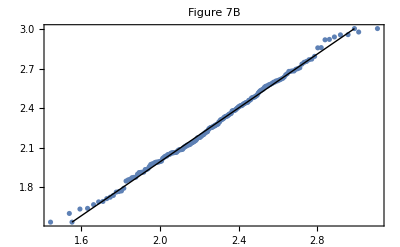

```mathematica
QuantilePlot[Log@varGroupB,PlotLabel->"Figure 7B"]
```

The quantile plots are the same as expected as the two transformation differ by a constant.

Finally, we use the Shapiro-Wilk test to determine if the transformed data is from a population in which the variable is normally distributed.  The p value is the same for both.

```mathematica
Map[ShapiroWilkTest,{Log10[varGroupB],Log[varGroupB]}]
```

{0.494469,0.494469}

### Square root transform

The square root transformation is used more often for ordinal data.  It is also only defined for positive data values.

Figure 8 show a histogram of the transformed data for group B.  The Sqrt function performs the square root transformation.

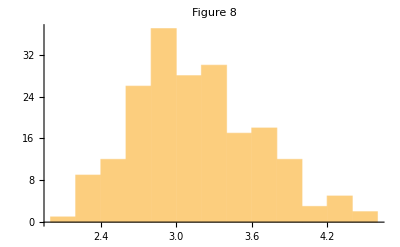

```mathematica
Histogram[Sqrt[varGroupB],PlotLabel->"Figure 8",ChartLegends->"Square root transformation"]
```

There is some positive skewness to the data.  The Shapiro-Wilk test shows a small p value and we reject the null hypothesis.

```mathematica
ShapiroWilkTest[Sqrt[varGroupB],"TestDataTable"]
```

### Comparing means

With the data transformed, we now use a t test to compare the means.  Figure 9 shows a box and whisker chart for the two groups.

```mathematica
ShapiroWilkTest[Log[varGroupA],"TestDataTable"]
```

| Statistic | P-Value
Shapiro-Wilk | 0.987605 | 0.0786253

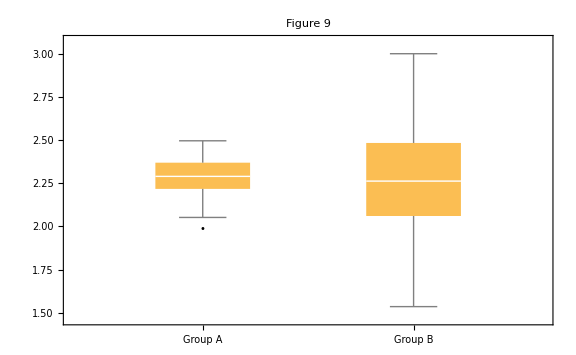

```mathematica
BoxWhiskerChart[{Log[varGroupA],Log[varGroupB]},"Outliers",PlotLabel->"Figure 9",ChartLabels->{"Group A","Group B"},ImageSize->Large]
```

The code cell below calculates the descriptive statistics for the log transform in both groups.

```mathematica
TableForm[describe/@{Log[varGroupA],Log[varGroupB]},TableHeadings->{None,{"Mean","Standard deviation","Median","Interquartile range"}}]
```

Mean | Standard deviation | Median | Interquartile range
2.29205 | 0.101987 | 2.2908 | 0.152136
2.27478 | 0.309333 | 2.2634 | 0.424042

Figure 10 shows the probability density functions for the two distributions given the mean and standard deviation from the descriptive statistics.

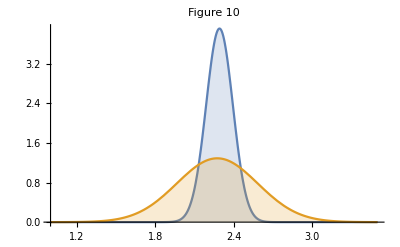

```mathematica
Show[Plot[PDF[NormalDistribution[2.29205,0.101987],x],{x,1,3.5},Filling->Axis,PlotRange->All,PlotLabel->"Figure 10"],Plot[{Orange,PDF[NormalDistribution[2.27478,0.309333],x]},{x,1,3.5},Filling->Axis,PlotRange->All]]
```

The TTest function performs a t test and is used for the transformed data.

```mathematica
TTest[{Log[varGroupA],Log[varGroupB]},0,"TestDataTable",VerifyTestAssumptions->"Normality"]
```

| Statistic | P-Value
T | 0.74945 | 0.454028

From the large p value, we cannot reject the null hypothesis.

The t test is fairly robust.  Below, we use it on the untransformed data.  The VerifyTestAssumptions parameter is set to None.  If set to All an error message will appear warning that one for the sets of data values is not from a distribution in which the variable is normally distributed.

```mathematica
TTest[{varGroupA,varGroupB},0,"TestDataTable",VerifyTestAssumptions->None]
```

| Statistic | P-Value
T | -1.07037 | 0.285102

It can be argued that data transformation should not be performed as nonparametric tests are available.  The Mann-Whitney test is shown below, using the MannWhitney function, and similarly does not reject the null hypothesis.

```mathematica
MannWhitneyTest[{varGroupA,varGroupB},0,"TestDataTable"]
```

| Statistic | P-Value
Mann-Whitney | 21218. | 0.292309